## Separated cutset finder

```mathematica
separatedcutsetfinder[vertices_,edges_,separation_,testdepth_]:=Module[
{midpoints,graph, midpointdistance,dualgraphindices,dualgraphedges,dualgraph,possiblecutsets,testedindependentsets,separatedcutsetindices,C,i,j},
(*Separetedcutsetfinder is a function to find edge cuts in a weighted graph. 
Inputs:  vertices - Set of vertices of the graph
	  edges - set of edges of the graph, input in the form v<->w
        separation -  real number strictly greater than 0, the desired
              separation of the returned cutset
		 testdepth - number of cutsets to look for before stopping

Outputs: A list of separated edge cutsets.
	.*)
	midpoints=edges;
        graph=Graph[vertices,edges];
(*Calculate the distances between midpoints of edges. Then find all pairs of midpoints which are distance less than separation apart. We can remove diagonal pairs from this as we do not want loops in the dual 
graph.*)
	midpointdistance=Table[
Min[GraphDistance[graph,i[[1]],j[[1]]]+1,GraphDistance[graph,i[[1]],j[[2]]]+1,GraphDistance[graph,i[[2]],j[[1]]]+1,GraphDistance[graph,i[[2]],j[[2]]]+1
],
{i,midpoints},{j,midpoints}];
     dualgraphindices=Position[midpointdistance,_?(#<separation&)];
     dualgraphindices=Complement[dualgraphindices,Flatten[Table[{i,j},{i,1,Length[midpoints]},{j,1,i}
],1]];

(*Define the dual graph edges and the dual graph. Find all independent vertex sets in the dual graph.*)
      dualgraphedges=Flatten[Table[{midpoints[[i[[1]]]]<->midpoints[[i[[2]]]]},{i,dualgraphindices}],1];     
      dualgraph=Graph[midpoints,dualgraphedges];
	possiblecutsets=FindIndependentVertexSet[dualgraph,Infinity,testdepth];
testiscutsetQ[test_]:=!ConnectedGraphQ[EdgeDelete[Graph[vertices,edges],test]];
(*Test all independent vertex sets for cutsets and find the independent sets that are cutsets.*)   
     testedindependentsets=
	Parallelize[Map[
	testiscutsetQ,possiblecutsets]
	]
;

      separatedcutsetindices=Flatten[Position[testedindependentsets,True]];
      C=Table[possiblecutsets[[i]],{i,separatedcutsetindices}]
]



separatedvertexcutsetfinder[vertices_,edges_,separation_,testdepth_]:=Module[
{graph, vertexdistance,dualgraphindices,dualgraphedges,dualgraph,possiblecutsets,testedindependentsets,separatedcutsetindices,cuts},
(*Separetedvertexcutfinder is a function to find vertex cuts in a weighted graph. 
Inputs:  vertices - Set of vertices of the graph
	  edges - set of edges of the graph, input in the form v<->w
		 separation -  real number strictly greater than 0, the desired
              separation of the returned cutset
		testdepth - number of cutsets to look for before stopping
Outputs: A list of separated vertex cutsets.
	
.*)

        graph=Graph[vertices,edges];
(*Calculate the distances between midpoints of edges. Then find all pairs of vertices which are distance less than separation apart. We can remove diagonal pairs from this as we do not want loops in the dual 
graph.*)
	vertexdistance=Table[GraphDistance[graph,α,β],{α,vertices},{β,vertices}];
     dualgraphindices=Position[vertexdistance,_?(#<separation&)];
     dualgraphindices=Complement[dualgraphindices,Flatten[Table[{i,j},{i,1,Length[vertices]}
,{j,1,i}],1]];

(*Define the dual graph edges and the dual graph. Find all independent vertex sets in the dual graph.*)
      dualgraphedges=Flatten[Table[{vertices[[α[[1]]]]<->vertices[[α[[2]]]]},{α,dualgraphindices}],1];     

dualgraph=Graph[vertices,dualgraphedges];

possiblecutsets=FindIndependentVertexSet[dualgraph,Infinity,testdepth];

testiscutsetQ[test_]:=!ConnectedGraphQ[VertexDelete[Graph[vertices,edges],test]];
(*Test all independent vertex sets for cutsets and find the independent sets that are cutsets.*)   
     testedindependentsets=
	Parallelize[Map[
	testiscutsetQ,possiblecutsets]
	]
;

      separatedcutsetindices=Flatten[Position[testedindependentsets,True]];
      cuts=Table[possiblecutsets[[i]],{i,separatedcutsetindices}]
]

specifiedseparatedvertexcutsetfinder[vertices_,edges_,separation_,vdes_,testdepth_]:=Module[
{graph, vertexdistance,dualgraphindices,dualgraphedges,mathedges,dualgraph,possiblecutsets,testedindependentsets,separatedcutsetindices,cuts},
(*Separetedvertexcutfinder is a function to find vertex cuts in a weighted graph containing a unique vertex, vdes. 
Inputs:  vertices - Set of vertices of the graph
	  edges - set of edges of the graph, input in the form v<->w
         weights - vector of weights of the edges, input the all ones 
			vector if using the combinatorial metric
		 separation -  real number strictly greater than 0, the desired
              separation of the returned cutset
		vdes - desired vertex to exist in the cutset
		testdepth - number of cutsets to look for before stopping
Outputs: A list of separated vertex cutsets containing vdes.
	
.*)
   graph=Graph[vertices,edges];

(*Calculate the distances between midpoints of edges. Then find all pairs of vertices which are distance less than separation apart. We can remove diagonal pairs from this as we do not want loops in the dual 
graph.*)
	vertexdistance=Table[GraphDistance[graph,α,β],{α,vertices},{β,vertices}];
     dualgraphindices=Position[vertexdistance,_?(#<separation&)];
     dualgraphindices=Complement[dualgraphindices,Flatten[Table[{i,j},{i,1,Length[vertices]},{j,1,i}],1]
];

(*Define the dual graph edges and the dual graph. Find all independent vertex sets in the dual graph.*)
      dualgraphedges=Flatten[Table[{vertices[[α[[1]]]]<->vertices[[α[[2]]]]},{α,dualgraphindices}],1];     
      dualgraph=Graph[vertices,dualgraphedges];

	possiblecutsets=FindIndependentVertexSet[{dualgraph,vdes},Infinity,testdepth];
testiscutsetQ[test_]:=!ConnectedGraphQ[VertexDelete[Graph[vertices,edges],test]];
(*Test all independent vertex sets for cutsets and find the independent sets that are cutsets.*)   
     testedindependentsets=
	Parallelize[Map[
	testiscutsetQ,possiblecutsets]
	]
;

      separatedcutsetindices=Flatten[Position[testedindependentsets,True]];
      cuts=Table[possiblecutsets[[i]],{i,separatedcutsetindices}]
]


specifiedseparatedcutsetfinder[vertices_,edges_,separation_,edes_,testdepth_]:=Module[
{primaryvertices,midpoints,halvededges,genvertices,graph,hweights, midpointdistance,dualgraphindices,dualgraphedges,dualgraph,possiblecutsets,testedindependentsets,separatedcutsetindices,C,i,j},
(*Separetedcutsetfinder is a function to find edge cuts in a weighted graph. 
Inputs:  vertices - Set of vertices of the graph
	  edges - set of edges of the graph, input in the form {v,w}
         weights - vector of weights of the edges, input the all ones 
			vector if using the combinatorial metric
		 separation -  real number strictly greater than 0, the desired
              separation of the returned cutset
		edes - the edge desired to lie in the cutsets
		testdepth - maximum number of searches for cutsets
Outputs: A list of separated edge cutsets containing edes.
	
.*)

(*halve the edges of the original graph by adding midpoints*)

	midpoints=edges;
    
(*Create the generalized halved graph: note that the weight of each edge is halved because
the edges are between midpoints and vertices*)
        graph=Graph[vertices,edges];

(*Calculate the distances between midpoints of edges. Then find all pairs of midpoints which are distance less than separation apart. We can remove diagonal pairs from this as we do not want loops in the dual 
graph.*)
	midpointdistance=Table[
Min[GraphDistance[graph,i[[1]],j[[1]]]+1,GraphDistance[graph,i[[1]],j[[2]]]+1,GraphDistance[graph,i[[2]],j[[1]]]+1,GraphDistance[graph,i[[2]],j[[2]]]+1
],
{i,midpoints},{j,midpoints}];
     dualgraphindices=Position[midpointdistance,_?(#<separation&)];
     dualgraphindices=Complement[dualgraphindices,Flatten[Table[{i,j},{i,1,Length[midpoints]},{j,1,i}
],1]];

(*Define the dual graph edges and the dual graph. Find all independent vertex sets in the dual graph.*)
      dualgraphedges=Flatten[Table[{midpoints[[i[[1]]]]<->midpoints[[i[[2]]]]},{i,dualgraphindices}],1];     
      dualgraph=Graph[midpoints,dualgraphedges];
	possiblecutsets=FindIndependentVertexSet[{dualgraph,edes},Infinity,testdepth];
testiscutsetQ[test_]:=!ConnectedGraphQ[EdgeDelete[Graph[vertices,edges],test]];
(*Test all independent vertex sets for cutsets and find the independent sets that are cutsets.*)   
     testedindependentsets=
	Parallelize[Map[
	testiscutsetQ,possiblecutsets]
	]
;

      separatedcutsetindices=Flatten[Position[testedindependentsets,True]];
      C=Table[possiblecutsets[[i]],{i,separatedcutsetindices}]
]
```

## Foster graph data

```mathematica
(* This section defines the relevant Foster graphs *)
(* The adjacency tables *)
F014data:={{1,2,3},{0,4,5},{0,6,7},{0,8,9},{1,10,11},{1,12,13},{2,10,12},{2,11,13},{3,11,12},{3,10,13},{4,6,9},{4,7,8},{5,6,8},{5,7,9}};
F016data:={{1,2,3},{0,4,5},{0,6,8},{0,7,9},{1,11,13},{1,10,12},{2,11,14},{3,10,14},{2,10,13},{3,11,12},{5,7,8},{4,6,9},{5,9,15},{4,8,15},{6,7,15},{12,13,14}};
F018data:={{1,2,3},{0,4,5},{0,6,7},{0,8,9},{1,10,12},{1,11,13},{2,11,14},{2,10,15},{3,13,15},{3,12,14},{4,7,17},{5,6,16},{4,9,16},{5,8,17},{6,9,17},{7,8,16},{11,12,15},{10,13,14}};
F024data:={{1,2,3},{0,4,5},{0,6,8},{0,7,9},{1,11,14},{1,10,13},{2,12,16},{3,12,15},{2,11,18},{3,10,17},{5,9,21},{4,8,20},{6,7,19},{5,19,23},{4,19,22},{7,20,23},{6,21,22},{9,20,22},{8,21,23},{12,13,14},{11,15,17},{10,16,18},{14,16,17},{13,15,18}}
F026data:={{1,2,3},{0,4,7},{0,6,9},{0,5,8},{1,10,13},{3,11,14},{2,12,15},{1,11,16},{3,12,17},{2,10,18},{4,9,22},{5,7,20},{6,8,21},{4,23,24},{5,24,25},{6,23,25},{7,21,23},{8,22,24},{9,20,25},{20,21,22},{11,18,19},{12,16,19},{10,17,19},{13,15,16},{13,14,17},{14,15,18}};
F040data:={{1,2,3},{0,4,5},{0,6,7},{0,8,9},{1,10,12},{1,11,13},{2,15,18},{2,14,19},{3,17,20},{3,16,21},{4,23,31},{5,22,30},{4,25,29},{5,24,28},{7,23,33},{6,22,32},{9,25,33},{8,24,32},{6,27,29},{7,26,28},{8,26,31},{9,27,30},{11,15,35},{10,14,34},{13,17,34},{12,16,35},{19,20,35},{18,21,34},{13,19,36},{12,18,36},{11,21,37},{10,20,37},{15,17,38},{14,16,38},{23,24,27},{22,25,26},{28,29,39},{30,31,39},{32,33,39},{36,37,38}};
F048data:={{1,2,3},{0,4,5},{0,6,8},{0,7,9},{1,11,17},{1,10,16},{2,13,21},{3,12,20},{2,15,19},{3,14,18},{5,23,25},{4,22,24},{7,23,29},{6,22,28},{9,22,27},{8,23,26},{5,27,31},{4,26,30},{9,25,35},{8,24,34},{7,28,33},{6,29,32},{11,13,14},{10,12,15},{11,19,43},{10,18,42},{15,17,47},{14,16,46},{13,20,45},{12,21,44},{17,40,46},{16,39,47},{21,41,43},{20,41,42},{19,40,44},{18,39,45},{43,45,46},{42,44,47},{39,40,41},{31,35,38},{30,34,38},{32,33,38},{25,33,37},{24,32,36},{29,34,37},{28,35,36},{27,30,36},{26,31,37}};

F014vertices:=Table[Subscript[v, i],{i,0,13}];
F016vertices:=Table[Subscript[v, i],{i,0,15}];
F018vertices:=Table[Subscript[v, i],{i,0,17}];
F024vertices:=Table[Subscript[v, i],{i,0,23}];
F026vertices:=Table[Subscript[v, i],{i,0,25}];
F040vertices=Table[Subscript[v, i],{i,0,39}];
F048vertices:=Table[Subscript[v, i],{i,0,47}];
F014edges:=Complement[Flatten[Table[{Subscript[v, i],Subscript[v, j]},{i,0,13},{j,F014data[[i+1]]}]],Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,13},{j,0,i-1}]]];
F016edges:=Complement[Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,15},{j,F016data[[i+1]]}]],Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,15},{j,0,i-1}]]];
F018edges:=Complement[Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,17},{j,F018data[[i+1]]}]],Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,17},{j,0,i-1}]]];
F024edges:=Complement[Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,23},{j,F024data[[i+1]]}]],Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,23},{j,0,i-1}]]];
F026edges:=Complement[Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,25},{j,F026data[[i+1]]}]],Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,25},{j,0,i-1}]]];
F040edges=Complement[Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,39},{j,F040data[[i+1]]}]],Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,39},{j,0,i-1}]]];
F048edges:=Complement[Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,47},{j,F048data[[i+1]]}]],Flatten[Table[{Subscript[v, i]<->Subscript[v, j]},{i,0,47},{j,0,i-1}]]];
F014=Graph[F014vertices,F014edges];
F016=Graph[F016vertices,F016edges];
F018=Graph[F018vertices,F018edges];
F024=Graph[F024vertices,F024edges];
F026=Graph[F026vertices,F026edges];
F040=Graph[F040vertices,F040edges];
F048=Graph[F048vertices,F048edges];
```

## Strongly edge separated graphs

```mathematica
(* This section deals with strongly edge separated graphs*)
```

```mathematica
(* The below finds a way to double check a graph is strongly separated by cutsets *)
(* Find neighbours of a vertex*)
neighbours[v_,graph_]:=VertexList[graph][[
Flatten[Position[
Table[
GraphDistance[graph,v,i],
{i,VertexList[graph]}],1
]]
]]

(* Check when a set of cutsets separates the vertices start1,start2 and wcheck *)
isseparating[graph_,start1_,start2_,wcheck_,cutset_]:=Min[
Flatten[
Table[
Min[
GraphDistance[EdgeDelete[graph,cutset],start1,wcheck],
GraphDistance[EdgeDelete[graph,cutset],start1,j],
GraphDistance[EdgeDelete[graph,cutset],start2,wcheck],GraphDistance[EdgeDelete[graph,cutset],start2,j]
],
{j,neighbours[wcheck,graph]}]]
]
(* Code to find vertices at distance at least 3 *)
gfar[v_,graph_]:=VertexList[graph][[Flatten[Position[Table[GraphDistance[graph,v,i],{i,VertexList[graph]}],_?(#>2&)]]]]

(* Checks whether start1 start2 is separated from all points at distance at least 3 from them by a set of cutsets by checking distance between them after removing edges in a cutset *)
strengthofcutsetlist[graph_,start1_,start2_,cutsets_]:=Table[
Max[
Table[
isseparating[graph,start1,start2,l,cutsets[[j]]],
{j,1,Length[cutsets]}]
],{l,Union[gfar[start1,graph],gfar[start2,graph]]}
]
```

```mathematica
(* Apply this to F040A*)

F040cuts=separatedcutsetfinder[F040vertices,F040edges,3,188527];
strengthofcutsetlist[F040,Subscript[v, 0],Subscript[v, 1],F040cuts]
Table[Subscript[e, ed[[1]][[2]],ed[[2]][[2]]],{i,1,Length[F040cuts]},{ed,F040cuts[[i]]}]

(* Apply this to the Gray Graph *)
ggvertices=GraphData["GrayGraph","Vertices"];
ggedges=GraphData["GrayGraph","Edges"];
ggweights=ConstantArray[1,Length[ggedges]];
gg=Graph[ggvertices,ggedges,VertexLabels->Automatic];
ggcuts=Union[
specifiedseparatedcutsetfinder[ggvertices,ggedges,3,1<->2,300000],specifiedseparatedcutsetfinder[ggvertices,ggedges,3,1<->54,300000],specifiedseparatedcutsetfinder[ggvertices,ggedges,3,25<->26 ,300000],specifiedseparatedcutsetfinder[ggvertices,ggedges,3,26<->27 ,300000]];
ggcutsshort=ggcuts[[Range[60]]];
strengthofcutsetlist[gg,1,26,ggcutsshort]
Table[Subscript[e, ed[[1]]-1,ed[[2]]-1],{i,1,Length[ggcutsshort]},{ed,ggcutsshort[[i]]}]
Length[ggcuts]
```

## F graphs vertex separated

{}

{}

{{v_3,v_5,v_6,v_14,v_18,v_20},{v_2,v_4,v_7,v_13,v_17,v_21},{v_1,v_8,v_9,v_15,v_16,v_19},{v_0,v_10,v_11,v_12,v_22,v_23}}

True

{{v_4,v_5,v_6,v_16,v_17,v_18},{v_3,v_7,v_9,v_15,v_19,v_24},{v_3,v_6,v_10,v_16,v_20,v_24},{v_3,v_6,v_7,v_13,v_18,v_22},{v_2,v_7,v_8,v_13,v_19,v_25},{v_2,v_4,v_11,v_17,v_21,v_25},{v_2,v_4,v_8,v_14,v_16,v_20},{v_1,v_8,v_9,v_14,v_19,v_23},{v_1,v_5,v_12,v_18,v_22,v_23},{v_1,v_5,v_9,v_15,v_17,v_21},{v_0,v_11,v_12,v_13,v_22,v_25},{v_0,v_10,v_12,v_14,v_20,v_23},{v_0,v_10,v_11,v_15,v_21,v_24}}

True

{{v_3,v_4,v_8,v_10,v_13,v_27,v_29,v_33,v_35,v_40,v_43,v_47},{v_2,v_5,v_9,v_11,v_12,v_26,v_28,v_32,v_34,v_39,v_42,v_46},{v_1,v_6,v_7,v_14,v_15,v_24,v_25,v_30,v_31,v_41,v_44,v_45},{v_0,v_16,v_17,v_18,v_19,v_20,v_21,v_22,v_23,v_36,v_37,v_38}}

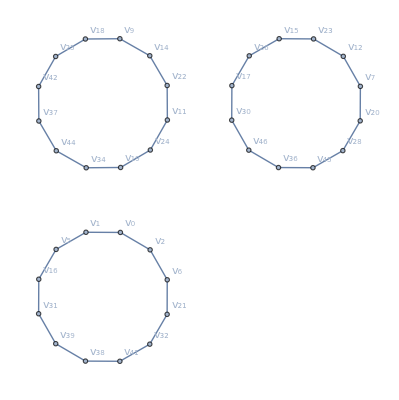

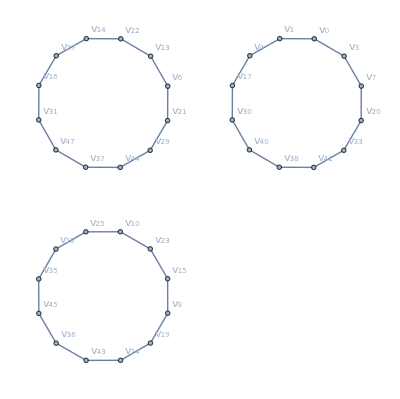

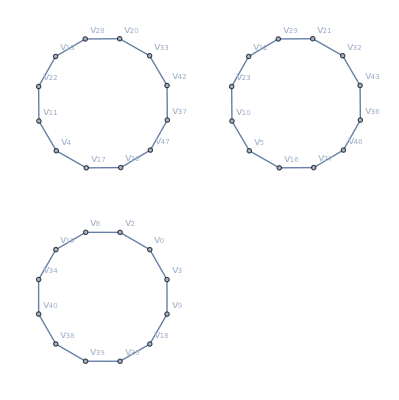

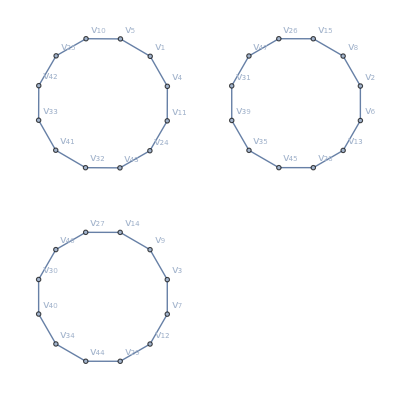

```mathematica
(* This section analyses vertex separation of some Foster graphs *)
F016cuts=separatedvertexcutsetfinder[F016vertices,F016edges,3,All]

F018cuts=separatedvertexcutsetfinder[F018vertices,F018edges,3,All]

F024cuts=separatedvertexcutsetfinder[F024vertices,F024edges,3,All]
Length[Complement[F024vertices,Flatten[F024cuts]]]==0


F026cuts=separatedvertexcutsetfinder[F026vertices,F026edges,3,All]
Length[Complement[F026vertices,Flatten[F026cuts]]]==0



(* Application to F048A *)
F048=Graph[F048vertices,F048edges];
(* Find points far from v1 *)
Table[GraphDistance[F048,Subscript[v, 1],i],{i,F048vertices}];
F048far=Flatten[Position[Table[GraphDistance[F048,Subscript[v, 1],i],{i,F048vertices}],_?(#>4&)]];

(* find cutsets *)
F048cuts=separatedvertexcutsetfinder[F048vertices,F048edges,3,All]

(* Nice pictures *)
VertexDelete[Graph[F048vertices,F048edges,VertexLabels->Automatic],F048cuts[[1]]]
VertexDelete[Graph[F048vertices,F048edges,VertexLabels->Automatic],F048cuts[[2]]]
VertexDelete[Graph[F048vertices,F048edges,VertexLabels->Automatic],F048cuts[[3]]]
VertexDelete[Graph[F048vertices,F048edges,VertexLabels->Automatic],F048cuts[[4]]]
```

## Minimal GQ

```mathematica
(* Apply this to the minimal generalized quadrangle*)
genquadvertices=Flatten[Table[{Subscript[u, i],Subscript[v, i]},{i,1,15}]];
genquadedges=Flatten[Union[Table[{Subscript[u, i]<->Subscript[v, i]},{i,15}],Table[{Subscript[u, i+1]<->Subscript[v, i]},{i,14}],{{Subscript[u, 1]<->Subscript[v, 15]}},{{Subscript[u, 1]<->Subscript[v, 9]},{Subscript[u, 2]<->Subscript[v, 5]},{Subscript[u, 3]<->Subscript[v, 7]},{Subscript[u, 4]<->Subscript[v, 12]},{Subscript[u, 5]<->Subscript[v, 8]},{Subscript[u, 6]<->Subscript[v, 10]},{Subscript[u, 7]<->Subscript[v, 15]},{Subscript[u, 8]<->Subscript[v, 11]},{Subscript[u, 9]<->Subscript[v, 13]},{Subscript[u, 10]<->Subscript[v, 3]},{Subscript[u, 11]<->Subscript[v, 14]},{Subscript[u, 12]<->Subscript[v, 1]},{Subscript[u, 13]<->Subscript[v, 6]},{Subscript[u, 14]<->Subscript[v, 2]},{Subscript[u, 15]<->Subscript[v, 4]}}]];
weights=ConstantArray[1,45];
genquadcuts=separatedcutsetfinder[genquadvertices,genquadedges,3,All];
Do[Print[genquadcuts[[11-i]]],{i,1,10}]
```

{u_1<->v_1,u_3<->v_2,u_4<->v_12,u_5<->v_5,u_7<->v_6,u_8<->v_11,u_9<->v_13,u_10<->v_10,u_15<->v_14}

{u_1<->v_1,u_6<->v_5,u_7<->v_7,u_9<->v_8,u_10<->v_3,u_11<->v_11,u_13<->v_12,u_14<->v_2,u_15<->v_4}

{u_1<->v_9,u_2<->v_2,u_4<->v_3,u_5<->v_8,u_6<->v_10,u_7<->v_7,u_12<->v_11,u_13<->v_13,u_15<->v_14}

{u_1<->v_9,u_2<->v_5,u_3<->v_3,u_7<->v_6,u_8<->v_8,u_11<->v_10,u_12<->v_12,u_14<->v_13,u_15<->v_4}

{u_1<->v_15,u_2<->v_2,u_5<->v_4,u_6<->v_6,u_8<->v_7,u_9<->v_13,u_10<->v_3,u_11<->v_14,u_12<->v_12}

{u_1<->v_15,u_2<->v_5,u_3<->v_7,u_4<->v_4,u_9<->v_8,u_10<->v_10,u_12<->v_11,u_13<->v_6,u_14<->v_14}

{u_2<->v_1,u_3<->v_3,u_5<->v_4,u_6<->v_10,u_7<->v_15,u_8<->v_11,u_9<->v_9,u_13<->v_12,u_14<->v_14}

{u_2<->v_1,u_3<->v_7,u_4<->v_12,u_5<->v_8,u_6<->v_6,u_10<->v_9,u_11<->v_11,u_14<->v_13,u_15<->v_15}

{u_3<->v_2,u_4<->v_4,u_6<->v_5,u_7<->v_15,u_8<->v_8,u_10<->v_9,u_11<->v_14,u_12<->v_1,u_13<->v_13}

{u_4<->v_3,u_5<->v_5,u_8<->v_7,u_9<->v_9,u_11<->v_10,u_12<->v_1,u_13<->v_6,u_14<->v_2,u_15<->v_15}